## Computing for Mathematical Physics 2022/23

# Homework 6

# Mark for homework 6: /38 (to be competed by your marker)

# Feedback from marker: (to be competed by your marker)

# Give your answers in the code cells marked (* Enter your solution here *)

Double click the vertical braces on the RHS of each of the question headings to open and view them.

1. FindRoot, NSolve, FindMinimum and FindMaximum.  [17 marks]

In the following we aim to compute the x values of all maxima and minima of the function

•  eq. 1 :   f(x) = BesselJ[0,x]+Sin[3x],

in the range  x_min<x<x_max,  with x_min=0 and x_max=π.

a) Set xMin=0 and xMax=π, and define a function f[x_] as per the definition above (eq. 1).
[0 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
xMin = 0
xMax = π
f[x_]:= BesselJ[0,x]+Sin[3x]
```

0

π

b) Plot the full extent of f(x), for x_min≤x≤x_max. Add a Frame to the plot, labelling the axes with FrameLabel, and add grid lines. Use LabelStyle to set the font colour, weight and family to black, bold and Courier respectively. 
[4 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

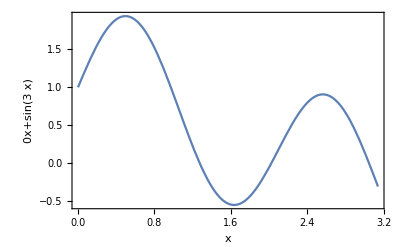

```mathematica
Plot[f[x], {x,xMin,xMax}, Frame->True,FrameLabel->{x,f[x]}, LabelStyle-> Directive[Black,Bold,FontFamily->"Courier"]]
```

c) Compute the derivative, d f/d x, and define a function fPrime[x_] returning the value of  d f/d x for a given input x. Display the numerical value of fPrime[2] to 4 s.f. only.
[1 mark]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
derivative=D[f[x],x]
fPrime[x_]:= -BesselJ[1,x]+3Cos[3 x]
N[fPrime[2],4]
```

-BesselJ[1,x]+3 Cos[3 x]

2.304

d) Use fPrime[x] to plot the full extent of d f/d x for  x_min<x<x_max with the same styling specified in b).
[2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

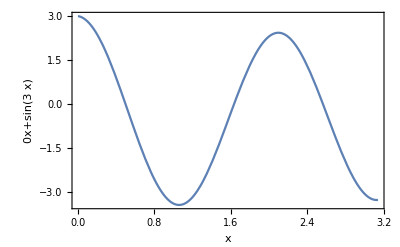

```mathematica
Plot[fPrime[x], {x,xMin,xMax}, Frame->True,FrameLabel->{x,f[x]}, LabelStyle-> Directive[Black,Bold,FontFamily->"Courier"]]
```

e) Use FindRoot together with fPrime[x] to compute the x-values of all maxima and minima of f(x) in x_min<x<x_max.
[4 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
FindRoot[fPrime[x]==0,{x,0.5}]
FindRoot[fPrime[x]==0,{x,1.6}]
FindRoot[fPrime[x]==0,{x,2.6}]
```

{x→0.496812}

{x→1.63487}

{x→2.56437}

f) Use FindMaximum and FindMinimum with f[x]to determine the x-values of all maxima and minima of f(x) in x_min<x<x_max.
[4 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
FindMaximum[f[x],{x,0.5}]
FindMinimum[f[x],{x,1.6}]
FindMaximum[f[x],{x,2.5}]
```

{1.93601,{x→0.496812}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-0.54611,{x→1.63487}}

{0.907232,{x→2.56437}}

g) Use NSolve to determine the x-values of all maxima and minima of f(x) in the same latter range.
[2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
NSolve[{fPrime[x]==0,xMin<=x<=xMax},x]
```

{{x→0.496812},{x→1.63487},{x→2.56437}}

2. FindRoot. [6 marks]

[If this question is proving difficult please move on to the next one and return here later.]

The code in the cell directly below this one makes a plot with the following two elements.

i) A green/yellow 3D surface, defined as function of x and y, with z coordinates given by the function

• surface[x_,y_]:=BesselJ[0,((x-1/6)^2+y^2)];

ii) A red wavy line, also in 3D, described by the following three parametric equations depending on the parameter x [which also happens to directly correspond to the x-coordinate here]:

•   [line x-coordinate]    xFn[x_] := x
•   [line y-coordinate]    yFn[x_] := 1/6 Sin[6 x]
•   [line z-coordinate]    zFn[x_] := 1/6 Cos[6 x]+1/6 x^2+1/2

The region of interest is defined as, -3≤x≤3, -3≤y≤3.

The output of the code is also included below for convenience. 

As you can see, the red wavy line intersects the green/yellow surface at just two points in the region of interest.

a) Use  FindRoot to determine the 3D coordinates of the two points where the red wavy line intersects the green/yellow surface, in the region of interest. Store these two points as firstPoint and secondPoint.

b) Make two Graphics3D[...] objects using Sphere[...], to display two 3D spheres with radius 1/5 centred on each of the two intersection points determined in part a), and insert these into the Show[...] command in the code given below.

[6 marks]

```mathematica
(* height/z-coordinate of surface as a function of x & y *)
surface[x_,y_]:=BesselJ[0,((x-1/6)^2+y^2)];

(* Parametric equation describing wavy line *)
xFn[x_]:=x
yFn[x_]:=1/6 Sin[6x]
zFn[x_]:=1/6 Cos[6x]+1/6 x^2+1/2

(* Region of interest *)
{xMin,xMax}={-3,3};
{yMin,yMax}={-3,3};

(* Making a combined 3D plot of the surface and line *)
Show[

(* Plot of green/yellow 3D surface *)
Plot3D[
(* Equation defining height of surface *)
(* as a function of x and y *)
surface[x,y],

(* Dependent variables and their ranges *)
{x,xMin,xMax},
{y,yMin,yMax},

(* Presentation *)
ColorFunction->"AvocadoColors",
PlotRange->{All,All,{-1/2,3/2}}
],

(* Plot of wavy red line in 3D *)
ParametricPlot3D[

(* Functions giving the line's x, y, and z *)
(* coordinates in terms of x *)
{xFn[x],yFn[x],zFn[x]},

(* Parameter x *)
{x,xMin,xMax},

(* Presentation *)
PlotStyle->{Red,Thickness[0.01]}
],

(* Presentation *)
PlotLabel->"Determining complex intersections with FindRoot",
AxesLabel->{"x","y","z"},
LabelStyle->{Black,Bold,14},
ImageSize->Large
]
```

-Graphics3D-

```mathematica
(* Enter code in a new cell immediately below this one. *)
firstX =FindRoot[{surface[x,yFn[x]] == zFn[x]}, {{x,1}}]
secondX=FindRoot[{surface[x,yFn[x]] == zFn[x]}, {{x,-1}}]
firstX=x/.firstX;
secondX = x/.secondX;
firstY=yFn[firstX];
firstZ = zFn[firstX];
secondY=yFn[secondX];
secondZ = zFn[secondX];
firstPoint = {firstX,firstY,firstZ}
secondPoint = {secondX,secondY,secondZ}

(* Making a combined 3D plot of the surface and line, this time repeated so no errors with variables called before being defined in a later cell *)
Show[
(* Adding Spheres to the Plot*)
Graphics3D[Sphere[firstPoint,1/5]],
Graphics3D[Sphere[secondPoint,1/5]],

(* Plot of green/yellow 3D surface *)
Plot3D[
(* Equation defining height of surface *)
(* as a function of x and y *)
surface[x,y],

(* Dependent variables and their ranges *)
{x,xMin,xMax},
{y,yMin,yMax},

(* Presentation *)
ColorFunction->"AvocadoColors",
PlotRange->{All,All,{-1/2,3/2}}
],

(* Plot of wavy red line in 3D *)
ParametricPlot3D[

(* Functions giving the line's x, y, and z *)
(* coordinates in terms of x *)
{xFn[x],yFn[x],zFn[x]},

(* Parameter x *)
{x,xMin,xMax},

(* Presentation *)
PlotStyle->{Red,Thickness[0.01]}
],

(* Presentation *)
PlotLabel->"Determining complex intersections with FindRoot",
AxesLabel->{"x","y","z"},
LabelStyle->{Black,Bold,14},
ImageSize->Large
]
```

{x→1.05319}

{x→-0.87696}

{1.05319,0.00599202,0.851427}

{-0.87696,0.142142,0.715201}

-Graphics3D-

3. Solving differential equations with DSolve and NDSolve.  [15 marks]

Consider the following differential equation
    • eq. 2    dy/dt = y^2/(1+t^2)
     with the boundary condition y(0) = 1.

a) Solve eq. 2, above, with its associated boundary condition, analytically, using DSolve, and store the solution as q3Analytic. [3 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
q3Analytic = Flatten[DSolve[{y'[t]==y[t]^2/(1+t^2), y[0]==1}, y[t], t]]
```

{y[t]→1/(1-ArcTan[t])}

b) Check the validity of the q3Analytic solution, by substituting the corresponding expressions for y(t) and y'(t) back into the original differential equation, eq. 2, using /. (ReplaceAll), and checking whether it reduces to True or not.  [4 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
D[y[t]/.q3Analytic,t]==y[t]^2/(1+t^2)/.q3Analytic
```

True

c) Repeat part a), but now using NDSolve in place of DSolve, to obtain a numerical solution over the range 0 ≤ t ≤ 1.5 . Store this solution as q3Numerical. [2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
q3Numerical=Flatten[NDSolve[{y'[t]==y[t]^2/(1+t^2), y[0]==1}, y[t], {t,0,1.5}]]
```

{y[t]→InterpolatingFunction[…][t]}

d) Plot the full extent of the q3Analytic y(t) solution, over the range 0 ≤ t ≤ 1.5. [2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

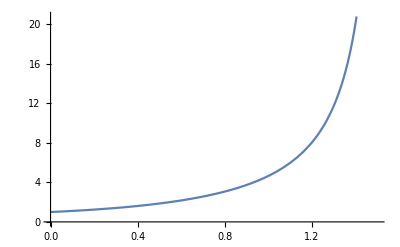

```mathematica
Plot[y[t]/.q3Analytic,{t,0,1.5}]
```

e) Plot the full extent of

     (y(t) from q3Numerical)/(y(t) from q3Analytic) - 1

     over the range 0 ≤ t ≤ 1.5. [2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

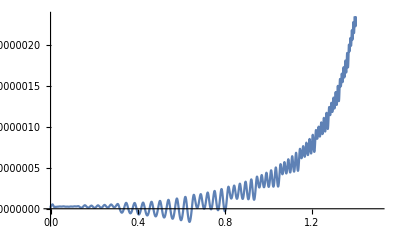

```mathematica
Plot[(y[t]/.q3Numerical)/(y[t]/.q3Analytic)-1, {t,0,1.5}]
```

f) Copy your code from parts c) and e) into a new cell. Increase the WorkingPrecision in NDSolve to 25, and plot again 

	(y(t) from q3Numerical)/(y(t) from q3Analytic) - 1

Explain, clearly, in one sentence, in a text cell, the effect of this option on the numerical solution from NDSolve.  [2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

{y[t]→InterpolatingFunction[…][t]}

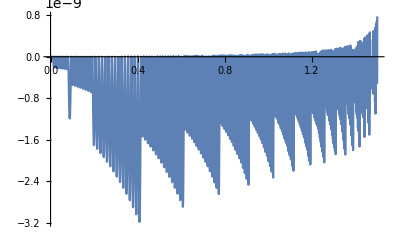

```mathematica
q3Numerical=Flatten[NDSolve[{y'[t]==y[t]^2/(1+t^2), y[0]==1}, y[t], {t,0,1.5}, WorkingPrecision->25]]
Plot[(y[t]/.q3Numerical)/(y[t]/.q3Analytic)-1, {t,0,1.5}]
```

Increasing the working precision has significantly reduced the difference between the numerical and analytical solutions, with the numerical solution no longer diverging from the analytical solution over the range of t we require the solution to function.

Total marks available: 38

Solutions are due by 1200 noon on Thursday March 2nd here:  allow time for uploading on moodle.

A 10% mark deduction will be made (4 marks) if the template isn’t used.

Name your solution notebook file in the format WK6_HMWK_<Initials>_<Family Name>.nb, e.g. WK6_HMWK_K_Hamilton.nb

Make a backup copy of your solutions.

Delete all cell evaluation output by selecting Cell → Delete All Output from the drop-down menus at the top of the screen, then save and upload that file to Moodle.

The first thing your marker will do when they receive your notebook is to evaluate all of it, to regenerate the output, by clicking Evaluation → Evaluate Notebook from the drop-down menus at the top of the screen. It is your responsibility to check that carrying out this process, with a fresh kernel, will produce the output you intend it to, before you upload your work.

K. Hamilton
15:18 21 Feb 2023